# Homework - 3 (CSCI - 561)

## DATASET 1 ( CIFAR - 100)

## Problem Statement

To experiment with various supervised learning algorithms on CIFAR - 100 dataset which consists of 50000 training images and which has been divided into 100 classes. And to analyze the behaviour of neural network , decision tree and Naive Bayes algorithms on the 10000 test images.

## The Dataset

The dataset has 100 classes containing 600 images each. There are 500 training images and 100 testing images per class. The 100 classes in the CIFAR-100 are grouped into 20 superclasses. Each image comes with a “fine” label (the class to which it belongs) and a “coarse” label (the superclass to which it belongs).
The dataset is imported as follows :

```mathematica
dataSet = ResourceObject["CIFAR-100"];
```

We can get the training data as follows :

```mathematica
trainingData = ResourceData[dataSet,"TrainingData"];
```

We can obtain the test data as follows :

```mathematica
testData = ResourceData[dataSet,"TestData"];
```

To obtain the number of classes in our training data, we perform the following operation:

```mathematica
classes=Union@Values[trainingData];
classes
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,31,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}
 |  |  |  |

## Data Preprocessing

The aim of data pre-processing is an improvement of the image data that suppresses unwanted distortions or enhances some image features important for further processing.
The pre-processing techniques i have used are applying gaussian filter with image subtract and Image Add.
I have reduced the training set from 50000 to 5000 images and reduced the test set from 10000 to 5000 images.

Gaussian Filter :

It is the result of blurring an image by a gaussian function. It is used to reduce the noise in an image.

When working with images, we need to use the two dimensional gaussian function. This is the product of two 1D gaussian functions.

Mathematica has an inbuilt function to apply gaussian filter for images. It is as follows : GaussianFilter[<image> , r] , where “r” is the radius of the kernal used.

#### Image Subtract :

The image returned by ImageSubtract[image,…] has the same dimensions as image.

In ImageSubtract[image,x], x can be a number normally in the range 0 to 1, a color, or a list of color channel values.

ImageSubtract[image,x] typically gives an image with the same underlying data type as image, clipping or truncating values if necessary.

Mathematica has a built in function for image subtract ImageSubtract[image,x] which subtracts a constant amount x from each channel value in image.

#### Image Add :

The image returned by ImageAdd[image,…] has the same dimensions as image.

In ImageAdd[image,x], x can be a number normally in the range 0 to 1, a color, or a list of color channel values.

ImageAdd[image,x] typically gives an image with the same underlying data type as image, clipping or truncating values if necessary.

Mathematica has a built in function for image add, ImageAdd[image,x] which adds a constant amount x from each channel value n image.

I have reduced the number of images in training and test dataset as shown below. I am picking 100 images from each class of training data and i am picking 30 images from each class of test data.
This results in a total of 10000 training images and 3000 test images.

```mathematica
random100TrainingData = {};
random100TestData = {};

For[i = 1, i <= 50000, i += 500, 
  random100TrainingData = 
   Join[random100TrainingData, 
    RandomSample[Take[trainingData, {i, i + 499}], 100]]];


flattenedTrainingData = Flatten[random100TrainingData];

For[i = 1, i <= 10000, i += 100, 
  random100TestData = 
   Join[random100TestData, 
    RandomSample[Take[testData, {i, i + 99}], 30]]];


flattenedTestData = Flatten[random100TestData];
```

I have used the above described three preprocessing methods together on reduced training and test data together  as follows :

```mathematica
imageAddSubtractGausian[x_] := 
 ImageAdd[x, ImageSubtract[x, GaussianFilter[x, 2]]];
 
 preprocessedTrainingData = Normal[KeyMap[imageAddSubtractGausian, <|flattenedTrainingData|>]];
 
 preprocessedTestData = Normal[KeyMap[imageAddSubtractGausian,<|flattenedTestData|>]];
```

```mathematica
Length[preprocessedTestData];
Length[preprocessedTrainingData];
trainingclasses=Union@Values[preprocessedTrainingData]
testclasses = Union@Values[preprocessedTrainingData]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,32,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}
 |  |  |  |

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,32,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}
 |  |  |  |

## Feature Extraction :

FeatureExtraction can be used on many types of data, including numerical, textual, sounds, and images, as well as combinations of these.

This is applied to the images in the training data set.

Once its done, this will return a Feature extractor function.

This feature extractor function will typically convert examples to numeric vectors, impute missing data, and reduce the dimension using DimensionReduction.

```mathematica
featureExtractionTrainingImages = Keys[preprocessedTrainingData];

fe = FeatureExtraction[featureExtractionTrainingImages];
```

## Classifiers :

We use classifiers to train our machine . We pass the pre-processed data , classifier method and the feature extractor function “ fe” to our Classifier. Below, i have explained 3 classifiers which i have used to train my machine to predict CIFAR-100 data.

### 1. Decision Trees :

A decision tree is a set of rules used to classify data into categories. It looks at the variables in a data set, determines which are most important, and then comes up with a tree of decisions which best partitions the data. The tree is created by splitting data up by variables and then counting to see how many are in each bucket after each split.

I have used random forest algorithm to implement decision trees.

#### Random Forest:

A random forest is simply a collection of decision trees whose results are aggregated into one final result.

Random forest algorithm does not over fit.

random forests are a strong modeling technique and much more robust than a single decision tree. They aggregate many decision trees to limit over fitting as well as error due to bias and therefore yield useful results.

I am running the classify function with the method as “Random Forest” and the performance goal as training speed

```mathematica
decisionFunction = Classify[preprocessedTrainingData,Method->"RandomForest",FeatureExtractor->fe];
```

### 2. Neural Network :

Artificial neural networks (ANNs)  are computing systems inspired by the biological neural networks that constitute animal brains. Such systems learn  to do tasks by considering examples. For example, in image recognition, they might learn to identify images that contain dogs by analyzing example images that have been manually labeled as “dog” or “no dog” and using the analytic results to identify dogs in other images.

Computations are structured in terms of an interconnected group of artificial neurons, processing information using a connectionist approach to computation. Modern neural networks are non-linear statistical data modeling tools. They are usually used to model complex relationships between inputs and outputs, to find patterns in data, or to capture the statistical structure in an unknown joint probability distribution between observed variables.

The original goal of the neural network approach was to solve problems in the same way that a human brain would. Over time, attention focused on matching specific mental abilities, leading to deviations from biology such as backpropagation, or passing information in the reverse direction and adjusting the network to reflect that information.

Neural networks have been used on a variety of tasks, including computer vision, speech recognition, machine translation, social network filtering, playing board and video games, medical diagnosis and in many other domains.

I am using Artificial Neural Network over Convolution neural network because this gave a higher accuracy. I have provided the comparisons below.

Here I am running the classify function with the method as “NeuralNetwork” and the performance goal as training speed inorder to reduce the training speed.

```mathematica
neuralFunction = Classify[preprocessedTrainingData,Method->"NeuralNetwork",FeatureExtractor->fe];
```

### 3. Naive Bayes :

Naive Bayes classifiers are a family of simple probabilistic classifiers based on applying Bayes’ theorem with strong (naive) independence assumptions between the features.

In simple terms, a Naive Bayes classifier assumes that the presence of a particular feature in a class is unrelated to the presence of any other feature.

Here I am running the classify function with the method as “Naive Bayes” and the performance goal as training speed inorder to reduce the training speed.

```mathematica
naiveFunction = Classify[preprocessedTrainingData,Method->"NaiveBayes",FeatureExtractor->fe];
```

## Findings :

### Convolution Neural Network:

No Pre-processing    -   36.30%

Image Substract with Gaussian Filter   -   38.4%

Laplacian Gaussian Filter - 35.5%

Edge detect - 19.10%

Image resize - 17.90%

Total Variation filter with deviation 0.25 - 36.95%

### Artificial Neural Network :

Feature Extractor with Dimension Reduction - 62.5%

Image Substract with Gaussian Filter - 62.85%

### Random Forest :

Feature Extractor with Dimension Reduction - 44%

Image Substract with Gaussian Filter - 52.8%

Total Variation Filter with deviation 0.25  - 50.67%

## Results:

### Decision Tree :

The classifier measurement function for decision tree is as follows :

```mathematica
decisionMeasure = ClassifierMeasurements[decisionFunction , preprocessedTestData];
```

```mathematica
Print[decisionMeasure]
```

ClassifierMeasurementsObject[…]

Accuracy of the classifier :

```mathematica
decisionAccuracy = decisionMeasure["Accuracy"];
Print[decisionAccuracy]
```

```mathematica
Print[decisionAccuracy]
```

0.471667

Precision of each class in the dataset :

```mathematica
decisionPrecision = decisionMeasure["Precision"];
Print[decisionPrecision]
```

<|apple→0.586957,aquarium fish→0.355263,baby→0.625,bear→0.,beaver→1.,bed→0.5,bee→0.4,beetle→0.425,bicycle→0.33871,bottle→0.464286,bowl→0.352941,boy→0.242424,bridge→0.333333,bus→0.357143,butterfly→0.5,camel→0.375,can→0.425,castle→0.436364,caterpillar→0.526316,cattle→0.315789,chair→0.54,chimpanzee→0.283582,clock→0.540541,cloud→0.5,cockroach→0.489362,computer keyboard→0.5,couch→0.5625,crab→0.4,crocodile→0.272727,cup→0.545455,dinosaur→0.461538,dolphin→0.375,elephant→0.294118,flatfish→1.,forest→0.395349,fox→0.372093,girl→0.304348,hamster→0.333333,house→0.611111,kangaroo→0.333333,lamp→0.857143,lawn-mower→0.588235,leopard→0.375,lion→0.358491,lizard→0.323529,lobster→0.333333,man→0.25,maple tree→0.4,motorcycle→0.677419,mountain→0.636364,mouse→0.333333,mushroom→0.357143,oak tree→0.385965,orange→0.674419,orchid→0.595238,otter→Indeterminate,palm tree→0.6,pear→0.666667,pickup truck→0.595238,pine tree→0.,plain→0.571429,plate→0.510638,poppy→0.513514,porcupine→0.217391,possum→0.321429,rabbit→0.5,raccoon→0.357143,ray→0.458333,road→0.615385,rocket→0.666667,rose→0.604651,sea→0.68,seal→0.307692,shark→0.590909,shrew→Indeterminate,skunk→0.422222,skyscraper→0.485714,snail→0.52381,snake→0.486486,spider→0.545455,squirrel→0.555556,streetcar→0.433333,sunflower→0.736842,sweet pepper→0.65,table→0.333333,tank→0.586207,telephone→0.684211,television→0.547619,tiger→0.666667,tractor→0.8,train→0.4,trout→0.53125,tulip→0.611111,turtle→0.619048,wardrobe→0.605263,whale→0.578947,willow tree→0.444444,wolf→1.,woman→0.666667,worm→0.541667|>

Recall of each class in the dataset :

```mathematica
decisionRecall = decisionMeasure["Recall"];
Print[decisionRecall];
```

<|apple→0.9,aquarium fish→0.9,baby→0.166667,bear→0.,beaver→0.1,bed→0.533333,bee→0.6,beetle→0.566667,bicycle→0.7,bottle→0.866667,bowl→0.2,boy→0.266667,bridge→0.133333,bus→0.5,butterfly→0.633333,camel→0.2,can→0.566667,castle→0.8,caterpillar→0.666667,cattle→0.4,chair→0.9,chimpanzee→0.633333,clock→0.666667,cloud→0.733333,cockroach→0.766667,computer keyboard→0.833333,couch→0.3,crab→0.466667,crocodile→0.1,cup→0.8,dinosaur→0.2,dolphin→0.6,elephant→0.333333,flatfish→0.133333,forest→0.566667,fox→0.533333,girl→0.233333,hamster→0.733333,house→0.366667,kangaroo→0.4,lamp→0.4,lawn-mower→0.666667,leopard→0.4,lion→0.633333,lizard→0.366667,lobster→0.0333333,man→0.533333,maple tree→0.466667,motorcycle→0.7,mountain→0.466667,mouse→0.0333333,mushroom→0.166667,oak tree→0.733333,orange→0.966667,orchid→0.833333,otter→0.,palm tree→0.8,pear→0.6,pickup truck→0.833333,pine tree→0.,plain→0.666667,plate→0.8,poppy→0.633333,porcupine→0.333333,possum→0.3,rabbit→0.0333333,raccoon→0.166667,ray→0.366667,road→0.8,rocket→0.666667,rose→0.866667,sea→0.566667,seal→0.266667,shark→0.433333,shrew→0.,skunk→0.633333,skyscraper→0.566667,snail→0.366667,snake→0.6,spider→0.4,squirrel→0.166667,streetcar→0.433333,sunflower→0.933333,sweet pepper→0.433333,table→0.0333333,tank→0.566667,telephone→0.866667,television→0.766667,tiger→0.2,tractor→0.266667,train→0.0666667,trout→0.566667,tulip→0.366667,turtle→0.433333,wardrobe→0.766667,whale→0.366667,willow tree→0.133333,wolf→0.133333,woman→0.133333,worm→0.433333|>

ROC curve for each class in the dataset:

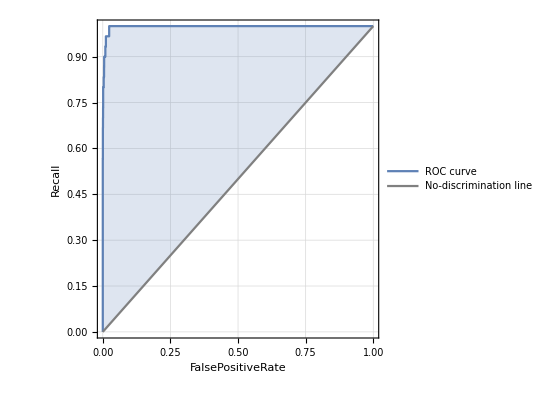
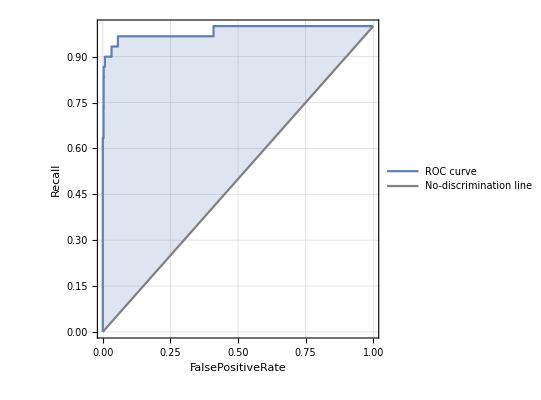
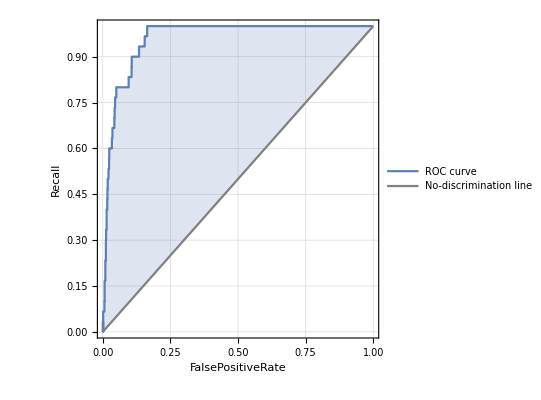
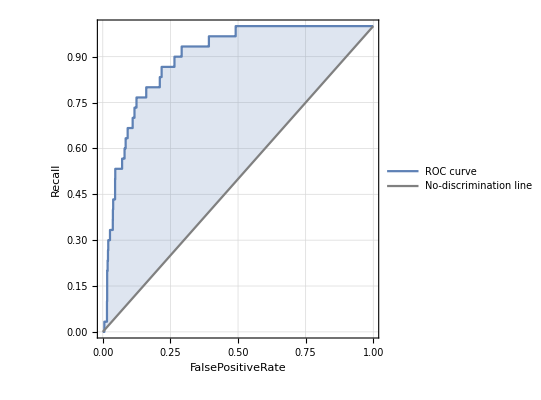
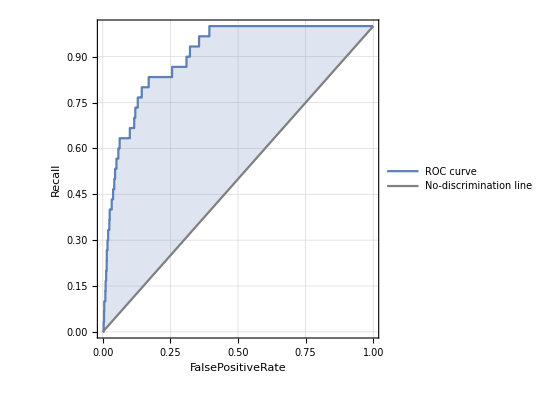
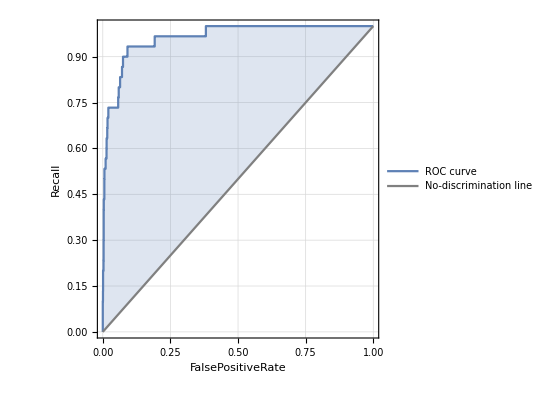
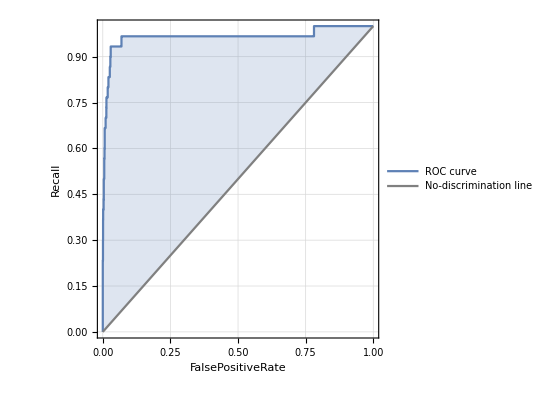
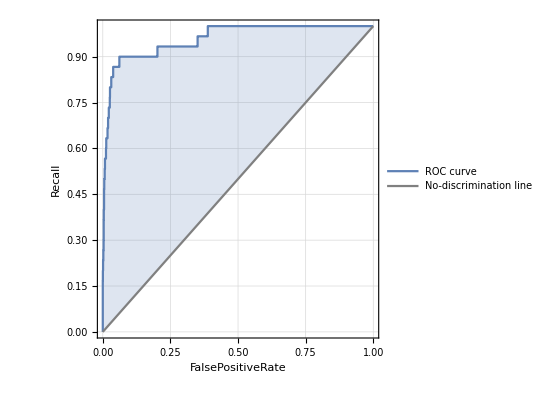
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
decisionROC = decisionMeasure["ROCCurve"];
Print[decisionROC]
```

### Neural Network :

The classfier measurement function for Neural network is as follows :

```mathematica
neuralMeasure = ClassifierMeasurements[neuralFunction , preprocessedTestData]
```

ClassifierMeasurementsObject[…]
 |  |  |  |

```mathematica
Print[neuralMeasure]
```

ClassifierMeasurementsObject[…]

Accuracy of the classifier :

```mathematica
neuralAccuracy = neuralMeasure["Accuracy"];
Print[neuralAccuracy];
```

0.589333

Precision of each class in the dataset :

```mathematica
neuralPrecision = neuralMeasure["Precision"];
Print[neuralPrecision];
```

<|apple→0.806452,aquarium fish→0.75,baby→0.5,bear→0.290323,beaver→0.212766,bed→0.6,bee→0.733333,beetle→0.68,bicycle→0.758621,bottle→0.88,bowl→0.44,boy→0.555556,bridge→0.6,bus→0.5,butterfly→0.774194,camel→0.444444,can→0.863636,castle→0.851852,caterpillar→0.666667,cattle→0.789474,chair→0.862069,chimpanzee→0.857143,clock→0.714286,cloud→0.666667,cockroach→0.894737,computer keyboard→0.675676,couch→0.363636,crab→0.705882,crocodile→0.526316,cup→0.827586,dinosaur→0.484848,dolphin→0.636364,elephant→1.,flatfish→0.555556,forest→0.5,fox→0.487179,girl→0.44,hamster→0.433962,house→0.85,kangaroo→0.571429,lamp→0.538462,lawn-mower→1.,leopard→0.545455,lion→0.809524,lizard→0.44186,lobster→0.354839,man→0.346939,maple tree→0.619048,motorcycle→0.628571,mountain→0.621622,mouse→0.392857,mushroom→0.75,oak tree→0.416667,orange→0.965517,orchid→0.827586,otter→0.255319,palm tree→0.833333,pear→0.85,pickup truck→0.869565,pine tree→0.44,plain→0.84,plate→0.583333,poppy→0.826087,porcupine→0.631579,possum→0.352941,rabbit→0.432432,raccoon→0.583333,ray→0.352941,road→0.961538,rocket→0.88,rose→0.71875,sea→0.76,seal→0.333333,shark→0.377049,shrew→0.333333,skunk→0.7,skyscraper→0.785714,snail→0.789474,snake→1.,spider→0.461538,squirrel→0.3125,streetcar→0.586207,sunflower→0.72973,sweet pepper→0.431034,table→0.638889,tank→0.625,telephone→0.605263,television→0.785714,tiger→0.761905,tractor→0.564103,train→0.625,trout→0.69697,tulip→0.714286,turtle→0.695652,wardrobe→0.682927,whale→0.652174,willow tree→0.423077,wolf→1.,woman→0.5,worm→0.364865|>

Recall of each class in the dataset :

```mathematica
neuralRecall = neuralMeasure["Recall"];
Print[neuralRecall]
```

<|apple→0.833333,aquarium fish→0.8,baby→0.5,bear→0.6,beaver→0.333333,bed→0.5,bee→0.733333,beetle→0.566667,bicycle→0.733333,bottle→0.733333,bowl→0.366667,boy→0.333333,bridge→0.6,bus→0.633333,butterfly→0.8,camel→0.666667,can→0.633333,castle→0.766667,caterpillar→0.666667,cattle→0.5,chair→0.833333,chimpanzee→0.6,clock→0.666667,cloud→0.733333,cockroach→0.566667,computer keyboard→0.833333,couch→0.533333,crab→0.4,crocodile→0.333333,cup→0.8,dinosaur→0.533333,dolphin→0.233333,elephant→0.166667,flatfish→0.5,forest→0.633333,fox→0.633333,girl→0.366667,hamster→0.766667,house→0.566667,kangaroo→0.4,lamp→0.7,lawn-mower→0.566667,leopard→0.4,lion→0.566667,lizard→0.633333,lobster→0.366667,man→0.566667,maple tree→0.433333,motorcycle→0.733333,mountain→0.766667,mouse→0.366667,mushroom→0.7,oak tree→0.5,orange→0.933333,orchid→0.8,otter→0.4,palm tree→0.833333,pear→0.566667,pickup truck→0.666667,pine tree→0.366667,plain→0.7,plate→0.7,poppy→0.633333,porcupine→0.4,possum→0.4,rabbit→0.533333,raccoon→0.466667,ray→0.6,road→0.833333,rocket→0.733333,rose→0.766667,sea→0.633333,seal→0.2,shark→0.766667,shrew→0.2,skunk→0.7,skyscraper→0.733333,snail→0.5,snake→0.233333,spider→0.8,squirrel→0.333333,streetcar→0.566667,sunflower→0.9,sweet pepper→0.833333,table→0.766667,tank→0.5,telephone→0.766667,television→0.733333,tiger→0.533333,tractor→0.733333,train→0.333333,trout→0.766667,tulip→0.5,turtle→0.533333,wardrobe→0.933333,whale→0.5,willow tree→0.366667,wolf→0.2,woman→0.433333,worm→0.9|>

ROC curve for each class in the dataset:

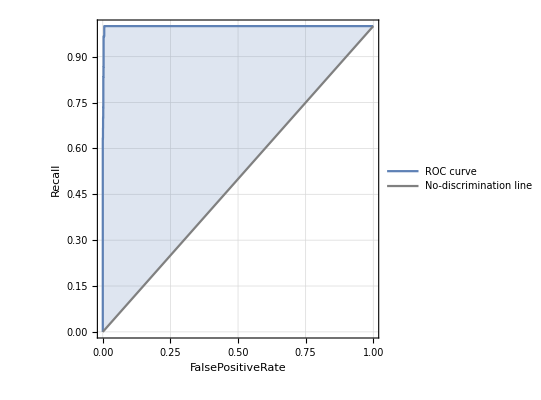
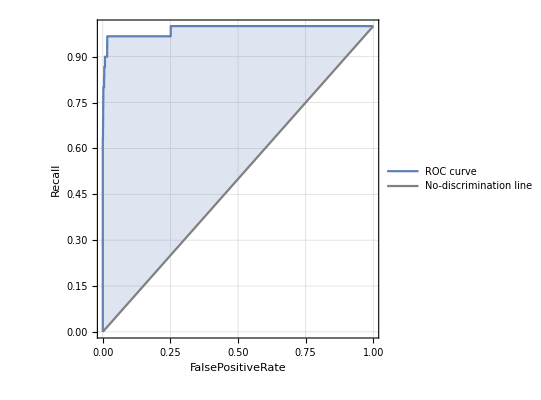
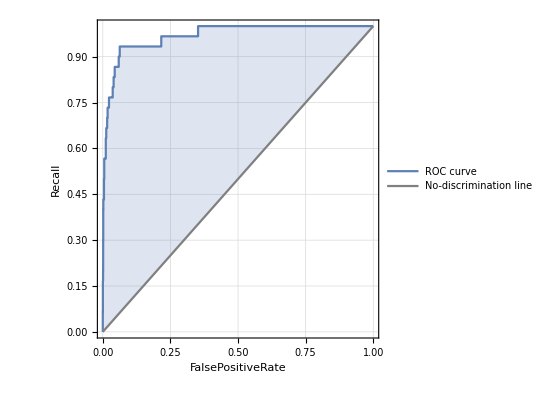
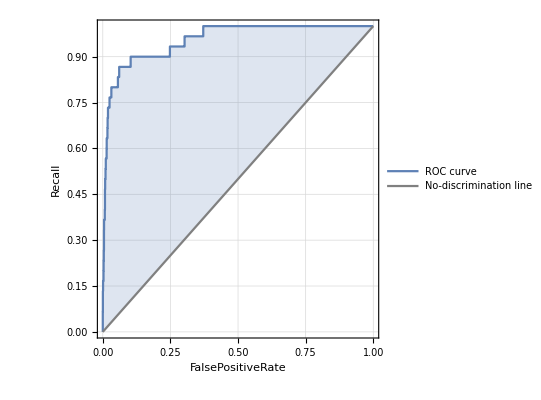
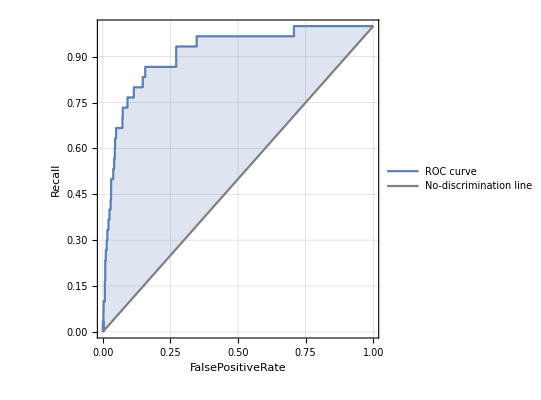
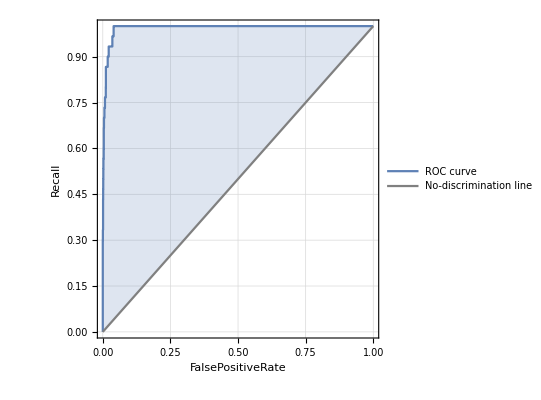
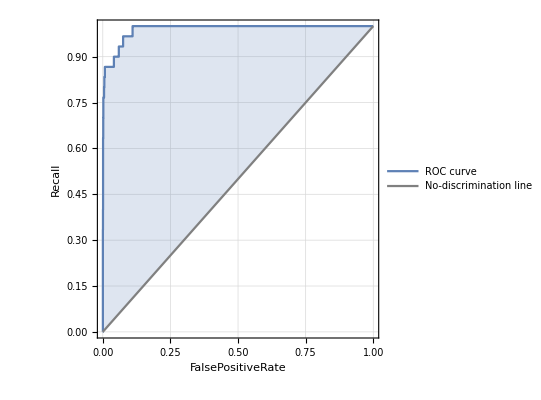
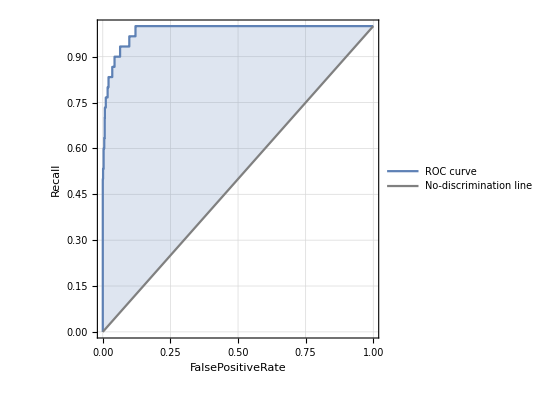
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
neuralROC = neuralMeasure["ROCCurve"];
Print[neuralROC];
```

### Naive Bayes :

The classifier measurement function for Naive Bayes is as follows :

```mathematica
naiveBayesMeasure = ClassifierMeasurements[naiveFunction , preprocessedTestData];
Print[naiveBayesMeasure]
```

ClassifierMeasurementsObject[…]

```mathematica
Print[naiveBayesMeasure]
```

ClassifierMeasurementsObject[…]

Accuracy of the classifier :

```mathematica
naiveAccuracy = naiveBayesMeasure["Accuracy"];
Print[naiveAccuracy];
```

0.560667

Precision of each class in the dataset :

```mathematica
naivePrecision = naiveBayesMeasure["Precision"];
Print[naivePrecision];
```

<|apple→0.827586,aquarium fish→0.814815,baby→0.307692,bear→0.241379,beaver→0.259259,bed→0.5,bee→0.730769,beetle→0.714286,bicycle→0.863636,bottle→0.952381,bowl→0.404762,boy→0.347826,bridge→0.269231,bus→0.631579,butterfly→0.769231,camel→0.454545,can→0.714286,castle→0.807692,caterpillar→0.692308,cattle→0.761905,chair→0.92,chimpanzee→0.814815,clock→0.772727,cloud→0.692308,cockroach→0.875,computer keyboard→0.888889,couch→0.423077,crab→0.521739,crocodile→0.232143,cup→0.846154,dinosaur→0.447368,dolphin→0.555556,elephant→0.419355,flatfish→0.357143,forest→0.447368,fox→0.666667,girl→0.333333,hamster→0.542857,house→0.76,kangaroo→0.541667,lamp→0.527778,lawn-mower→0.826087,leopard→0.4,lion→0.589744,lizard→0.464286,lobster→0.271186,man→0.309524,maple tree→0.666667,motorcycle→0.666667,mountain→0.607143,mouse→0.375,mushroom→0.5,oak tree→0.422222,orange→0.896552,orchid→0.8,otter→0.428571,palm tree→0.702703,pear→0.666667,pickup truck→0.772727,pine tree→0.37931,plain→0.826087,plate→0.68,poppy→0.708333,porcupine→0.411765,possum→0.296296,rabbit→0.5625,raccoon→0.457143,ray→0.423077,road→0.892857,rocket→0.636364,rose→0.78125,sea→0.666667,seal→0.263158,shark→0.481481,shrew→0.2,skunk→0.545455,skyscraper→0.75,snail→0.586207,snake→0.59375,spider→0.777778,squirrel→0.307692,streetcar→0.522727,sunflower→0.903226,sweet pepper→0.515152,table→0.465116,tank→0.653846,telephone→0.793103,television→0.65,tiger→0.452381,tractor→0.395833,train→0.361111,trout→0.703704,tulip→0.565217,turtle→0.714286,wardrobe→0.884615,whale→0.55,willow tree→0.45,wolf→0.592593,woman→0.366667,worm→0.68|>

Recall of each class in the dataset :

```mathematica
naiveRecall = naiveBayesMeasure["Recall"];
Print[naiveRecall];
```

<|apple→0.8,aquarium fish→0.733333,baby→0.4,bear→0.233333,beaver→0.233333,bed→0.566667,bee→0.633333,beetle→0.666667,bicycle→0.633333,bottle→0.666667,bowl→0.566667,boy→0.266667,bridge→0.466667,bus→0.4,butterfly→0.666667,camel→0.5,can→0.833333,castle→0.7,caterpillar→0.6,cattle→0.533333,chair→0.766667,chimpanzee→0.733333,clock→0.566667,cloud→0.6,cockroach→0.7,computer keyboard→0.8,couch→0.366667,crab→0.4,crocodile→0.433333,cup→0.733333,dinosaur→0.566667,dolphin→0.666667,elephant→0.433333,flatfish→0.5,forest→0.566667,fox→0.533333,girl→0.466667,hamster→0.633333,house→0.633333,kangaroo→0.433333,lamp→0.633333,lawn-mower→0.633333,leopard→0.466667,lion→0.766667,lizard→0.433333,lobster→0.533333,man→0.433333,maple tree→0.333333,motorcycle→0.666667,mountain→0.566667,mouse→0.2,mushroom→0.533333,oak tree→0.633333,orange→0.866667,orchid→0.8,otter→0.2,palm tree→0.866667,pear→0.733333,pickup truck→0.566667,pine tree→0.366667,plain→0.633333,plate→0.566667,poppy→0.566667,porcupine→0.233333,possum→0.266667,rabbit→0.3,raccoon→0.533333,ray→0.366667,road→0.833333,rocket→0.7,rose→0.833333,sea→0.466667,seal→0.5,shark→0.433333,shrew→0.1,skunk→0.6,skyscraper→0.8,snail→0.566667,snake→0.633333,spider→0.7,squirrel→0.266667,streetcar→0.766667,sunflower→0.933333,sweet pepper→0.566667,table→0.666667,tank→0.566667,telephone→0.766667,television→0.866667,tiger→0.633333,tractor→0.633333,train→0.433333,trout→0.633333,tulip→0.433333,turtle→0.5,wardrobe→0.766667,whale→0.366667,willow tree→0.3,wolf→0.533333,woman→0.366667,worm→0.566667|>

ROC curve for each class in the dataset:

```mathematica
naiveROC = naiveBayesMeasure["ROCCurve"];
Print[naiveROC];
```

<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

## Conclusions:

Finally by comparing the results of all the three machine learning techniques, i conclude by saying that naive-bayes and neural network image classifiers are better than decision tree with random forest classifier for CIFAR-100 dataset